frequency = 22.5 khz

513

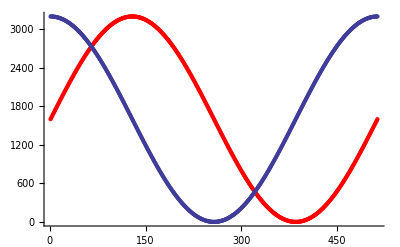

```mathematica
Clear["Global`*"]
maxVal=3200;
frequency=1000/(1.0/72*maxVal);  (* khz *)
Print["frequency = ",frequency," khz"]
step =128*4;
max=maxVal/2;
angle=360;
d1=Table[Floor[(Sin[x Degree]+1)*max+0.5],{x,0,angle,angle/(step)}];
d2=Table[Floor[(Cos[x Degree]+1)*max+0.5],{x,0,angle,angle/(step)}];
Length[d1]
Show[
ListPlot[d1,PlotStyle->Red],
ListPlot[d2]]
```